```mathematica
(**Size of the interval**)
```

```mathematica
lambda=1
```

1

```mathematica
(**Definition of the test function**)
```

```mathematica
u[x_]:=If[x^2<lambda^2,1/Sqrt[-Log[(lambda^2-x^2)/(2*lambda^2)]],0]
```

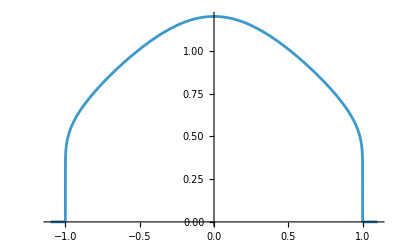

```mathematica
Plot[u[x],{x,-lambda-0.1,lambda+0.1},PlotRange->All,Exclusions->None]
```

```mathematica
(**Definition of the Logarithmic Laplacian**)
```

```mathematica
rho1=2*Log[2]+Gamma'[1/2]/Gamma[1/2]-EulerGamma
```

-EulerGamma+2 Log[2]+PolyGamma[0,1/2]

```mathematica
LapLog[x_]:=NIntegrate[(u[x]-u[y])/Abs[x-y],{y,x-1,x+1}]-NIntegrate[u[y]/Abs[x-y],{y,-Infinity,x-1}]-NIntegrate[u[y]/Abs[x-y],{y,x+1,Infinity}]+rho1*u[x]
```

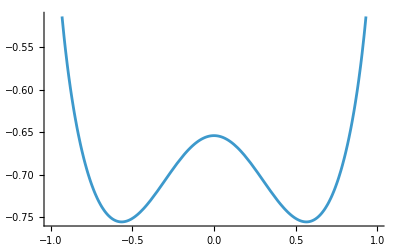

```mathematica
B=Plot[LapLog[x],{x,-lambda,lambda}]
```

```mathematica
(**Number of subintervals for the mesh**)
```

```mathematica
n=50;
```

```mathematica
(**Value of the logarithmic Laplacian at (almost) the ends of the interval**)
```

```mathematica
ll1=LapLog[-lambda+0.00000000001];
```

```mathematica
(**Table of values for the logarithmic Laplacian**)
```

```mathematica
l=Table[{N[-lambda+m(2*lambda/(n+1))],LapLog[-lambda+m(2*lambda/(n+1))]},{m,1,n}];
l=Append[l,{lambda,ll1}];
l=Prepend[l,{-lambda,ll1}];
```

```mathematica
(**Command to export the Table to a file recognized by MatLab**)
```

```mathematica
Export["~/Desktop/file50_lambda3.txt",l,"Table"];
```

```mathematica
l
```

{{-1,0.0482033},{-0.666667,-0.74374},{-0.333333,-0.716121},{0.,-0.654062},{0.333333,-0.716121},{0.666667,-0.74374},{1,0.0482033}}

```mathematica
ftilde=Interpolation[l,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
(NIntegrate[(LapLog[x]-ftilde[x])^2,{x,-lambda+0.00000000001,lambda-0.00000000001}])^(1/2)
```

NIntegrate::nlim: y = -1.+x is not a valid limit of integration.

NIntegrate::inumr: The integrand If[y^2<1,1/(√(-Log[Times[«2»]])),0]/Abs[x-y] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,-1.+x}}.

NIntegrate::inumr: The integrand If[y^2<1,1/(√(-Log[Times[«2»]])),0]/Abs[x-y] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,1.+x}}.

NIntegrate::nlim: y = -1.+x is not a valid limit of integration.

NIntegrate::inumr: The integrand If[y^2<1,1/(√(-Log[Times[«2»]])),0]/Abs[x-y] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,1.+x}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::nlim: y = -1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

0.0471768

```mathematica
(**Errores de f y ftilde**)
```

```mathematica
(**Number of subintervals for the mesh**)
```

```mathematica
n=1600;
```

```mathematica
(**Value of the logarithmic Laplacian at (almost) the ends of the interval**)
```

```mathematica
ll1=LapLog[-lambda+0.00000000001];
```

```mathematica
(**Table of values for the logarithmic Laplacian**)
```

```mathematica
l=Table[{N[-lambda+m(2*lambda/(n+1))],LapLog[-lambda+m(2*lambda/(n+1))]},{m,1,n}];
l=Append[l,{lambda,ll1}];
l=Prepend[l,{-lambda,ll1}];
```

```mathematica
ftilde=Interpolation[l,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
a1600=(NIntegrate[(LapLog[x]-ftilde[x])^2,{x,-lambda+0.00000000001,lambda-0.00000000001}])^(1/2);
```

NIntegrate::nlim: y = -1.+x is not a valid limit of integration.

NIntegrate::inumr: The integrand If[y^2<1,1/(√(-Log[Times[«2»]])),0]/Abs[x-y] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,-1.+x}}.

NIntegrate::inumr: The integrand If[y^2<1,1/(√(-Log[Times[«2»]])),0]/Abs[x-y] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,1.+x}}.

NIntegrate::nlim: y = -1.+x is not a valid limit of integration.

NIntegrate::inumr: The integrand If[y^2<1,1/(√(-Log[Times[«2»]])),0]/Abs[x-y] has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,1.+x}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::nlim: y = -1.-1. x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.998365329137526132108337861836844240315258502960205078125}. NIntegrate obtained 0.0000113607 and 3.06682×10^-9 for the integral and error estimates.

```mathematica
{a50,a100,a200,a400,a800,a1600}
```

{0.0471768,0.0294822,0.0185489,0.0117393,0.00746598,0.00337056}

```mathematica
f[t_]:=Sqrt[t]
```

```mathematica
g[t_]:=t^(0.6)
```

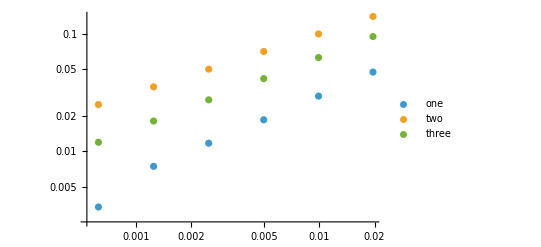

```mathematica
ListLogLogPlot[{{{1/51,a50},{1/101,a100},{1/201,a200},{1/401,a400},{1/801,a800},{1/1601,a1600}},{{1/51,f[1/51]},{1/101,f[1/101]},{1/201,f[1/201]},{1/401,f[1/401]},{1/801,f[1/801]},{1/1601,f[1/1601]}},{{1/51,g[1/51]},{1/101,g[1/101]},{1/201,g[1/201]},{1/401,g[1/401]},{1/801,g[1/801]},{1/1601,g[1/1601]}}},PlotLegends->{"one","two","three"}]
```

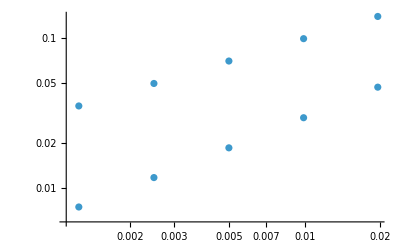

```mathematica
ListLogLogPlot[{{1/51,a50},{1/101,a100},{1/201,a200},{1/401,a400},{1/801,a800},{1/51,f[1/51]},{1/101,f[1/101]},{1/201,f[1/201]},{1/401,f[1/401]},{1/801,f[1/801]}}]
```

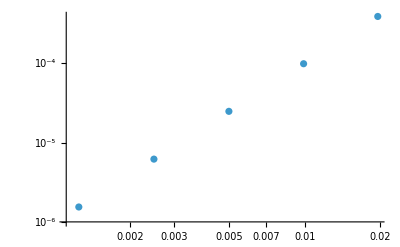

```mathematica
Q1=ListLogLogPlot[{{1/51,1/51^2},{1/101,1/101^2},{1/201,1/201^2},{1/401,1/401^2},{1/801,1/801^2}}]
```

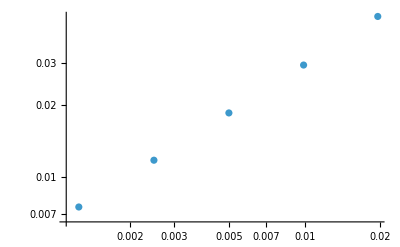

```mathematica
Show[Q2,Q1]
```

```mathematica
data={{1/51,a50},{1/101,a100},{1/201,a200},{1/401,a400},{1/801,a800},{1/1601,a1600}}
```

{{1/51,0.0471768},{1/101,0.0294822},{1/201,0.0185489},{1/401,0.0117393},{1/801,0.00746598},{1/1601,0.00337056}}

```mathematica
logX=Log[data[[All,1]]];
logY=Log[data[[All,2]]];
slopes=Differences[logY]/Differences[logX];
```

```mathematica
slopes
```

{0.688016,0.673331,0.662368,0.654118,1.14838}

```mathematica
L=1
```

1

```mathematica
Lk=8.6461
```

8.6461

```mathematica
2*Log[Lk/L]
```

4.31422